## Outtake

### Make bar chart logarithmic Put scales for years as well Put years on left, totals on right, names in the center Use blue for bar chart

For Developer

```mathematica
(*See GoL-10-Data* for retrieval code*) 
namesdiscoverers = Select[, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, "Discovered by"]];
```

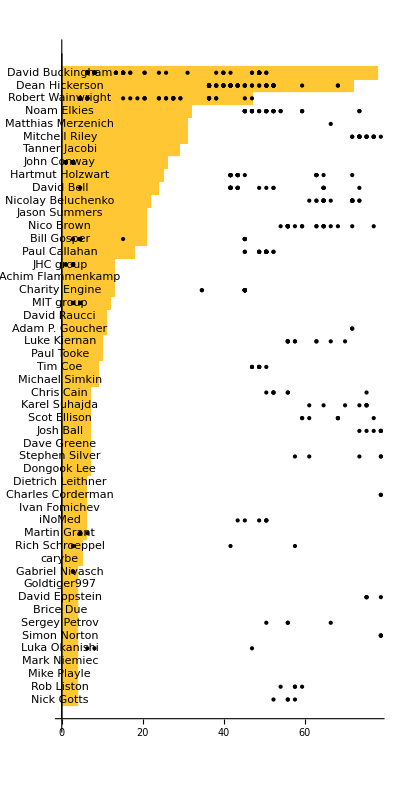

```mathematica
BarChart[Take[Sort[Counts[namesdiscoverers]],-50],ChartLabels->Placed[Keys[Take[Sort[Counts[namesdiscoverers]],-50]],Axis,(*Style[Rotate[#,Pi/2],6]*)#&],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None,Epilog->Point[{Rescale[ToExpression[#1],{1969,2025},{1,100}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[goodData,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&]]]
```

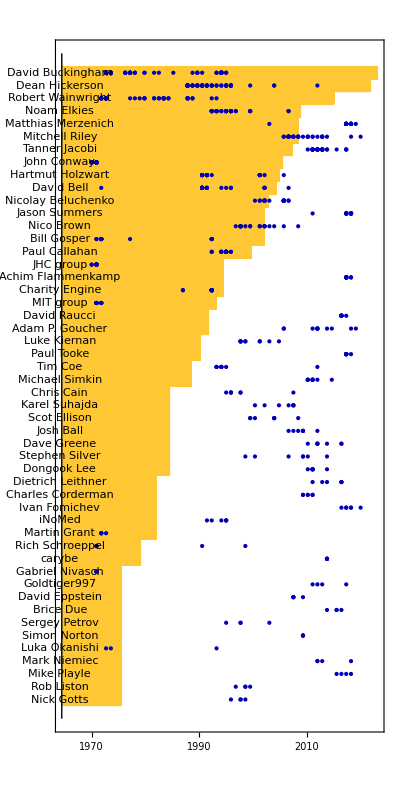

```mathematica
Show[BarChart[KeyValueMap[Labeled[#2, #1, Axis]&,Take[Sort[Counts[namesdiscoverers]],-50]],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None, ScalingFunctions->"Log2"], Graphics[{ RGBColor[0, 0, 0.73], Point[{Rescale[ToExpression[#1],{1969,2025},{1.5,6}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[, KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&]]}],Axes-> True, Frame->(*False *){True, False, True, False}, FrameTicks-> {{None, None}, {Transpose[{Subdivide[1.5, 6, 5], Range[1970, 2020, 10]}], Table[{i, 2^i}, {i,2, 6}]}}]
```

```mathematica
2^6
```

64

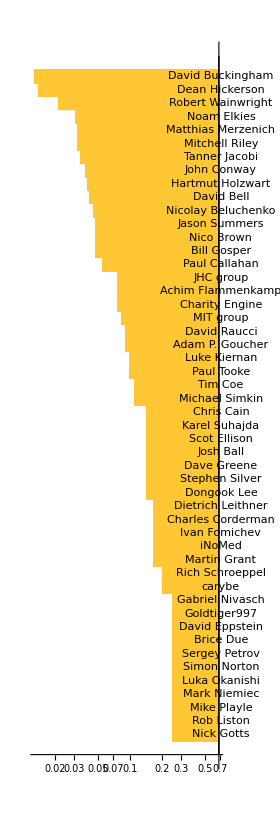
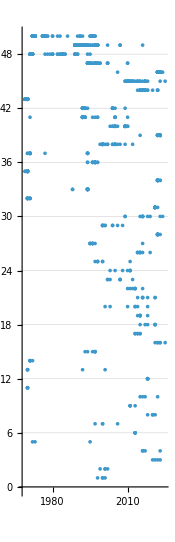

```mathematica
Row[{BarChart[Take[Sort[Counts[namesdiscoverers]],-50], BarOrigin->Right, ScalingFunctions->"Log", AspectRatio->3, ImageSize->280, PlotRangePadding->{Automatic, .8}, ChartLabels->(Style[Text[#],TextAlignment->Center]&)/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]]], ListPlot[{ToExpression[#1],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[Reverse@{First[#2], #1}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&],  AspectRatio->3.1, ImageSize->175,PlotRangePadding->{Automatic, {None, 1.8}}, PlotStyle-> PointSize[.015](*, Frame-> {False, False, True, False}, FrameTicks->Range[1969, 2025]*), Axes->{True, False}, GridLines->{None, Range[.5, 50.5, 1]}]}, Alignment->Top]
```

## Updates

### Making getvector

```mathematica
allsimps = Table[Module[{p3=SortBy[Select[$LifeData,#Class==="Spaceship"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

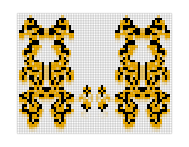
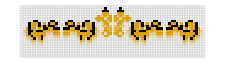
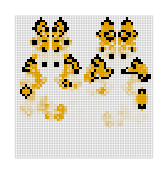
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]]&,Catenate[allsimps]]
```

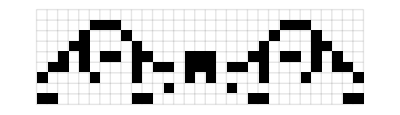
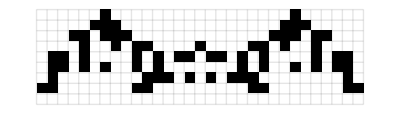
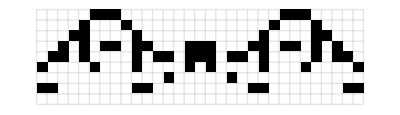

```mathematica
(ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.1]]& /@
CellularAutomaton["GameOfLife",{#MatrixData,0},#Period])&@allsimps[[1, 1]]
```

```mathematica
(ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.1]]& /@
CellularAutomaton["GameOfLife",{#MatrixData,0},{20 ,{-5, 10}, {-5, 35}}])&@allsimps[[1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Max[Position[CellularAutomaton["GameOfLife",{#MatrixData,0},{10 ,{-5, 10}, {-5, 35}}]&@allsimps[[1, 1]], 1]]
```

36

```mathematica
MaximalBy[Position[#, 1], First,1][[1, 1]]&/@CellularAutomaton["GameOfLife",{#MatrixData,0},{10 ,{-5, 10}, {-5, 35}}]&@allsimps[[1, 1]]
```

{13,12,12,11,11,10,10,9,9,8,8}

```mathematica
$LifeData[""]
```

```mathematica
CoordinateBounds[Position[CellularAutomaton["GameOfLife",{#MatrixData,0},{10 ,{-5, 10}, {-5, 35}}]&@allsimps[[1, 1]], 1]]
```

{{1,11},{1,13},{6,36}}

```mathematica
(CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{#MatrixData,0},{10 ,{-5, 10}, {-5, 35}}]&@allsimps[[1, 1]]))
```

{{{6,6},{13,36}},{{5,6},{12,36}},{{5,6},{12,36}},{{4,6},{11,36}},{{4,6},{11,36}},{{3,6},{10,36}},{{3,6},{10,36}},{{2,6},{9,36}},{{2,6},{9,36}},{{1,6},{8,36}},{{1,6},{8,36}}}

```mathematica
Differences[(CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{#MatrixData,0},{10 ,{-5, 10}, {-5, 35}}]&@allsimps[[1, 1]]))]
```

{{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}}}

```mathematica
Reverse[First[Total[#]/Length[#]]]*-1&[Differences[(CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{#MatrixData,0},{10 ,{-5, 10}, {-5, 35}}]&@allsimps[[1, 1]]))]]
```

{0,1/2}

```mathematica
{{6,6},{13,36}} - {{5,6},{12,36}}
```

{{1,0},{1,0}}

```mathematica
ClearAll@getvector
getvector[data_, t_:Automatic]:= Reverse[First[Total[#]/Length[#]]]*-1&[Differences[(CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{data["MatrixData"],0},If[t === Automatic, Min[5data["Period"], 5000], t]]))]]
```

```mathematica
allsimps[[2,2]]
```

<|Name→84P3H1V0.1,Year→1989,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/84P3H1V0.1,DataFiles→{84p3h1v0.1.cells,84p3h1v0.1.rle},MatrixData→SparseArray[Automatic,{8,41},0,{1,{{0,4,24,36,50,68,74,80,84},{{8},{15},{27},{34},{6},{7},{8},{9},{10},{14},{15},{17},{18},{19},{23},{24},{25},{27},{28},{32},{33},{34},{35},{36},{2},{3},{4},{6},{13},{20},{22},{29},{36},{38},{39},{40},{1},{10},{12},{13},{14},{18},{20},{22},{24},{28},{29},{30},{32},{41},{2},{5},{11},{13},{14},{15},{18},{19},{20},{22},{23},{24},{27},{28},{29},{31},{37},{40},{6},{17},{18},{24},{25},{36},{4},{5},{17},{25},{37},{38},{15},{17},{25},{27}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→84|>

```mathematica
Map[getvector, Take[allsimps, 1], {2}]
```

10

{{{0,1/2}}}

```mathematica
Map[#Speed&, allsimps, {2}]
```

{{1/2},{1/3,1/3,1/3},{1/4},{2/5,2/5},{1/6,1/3,1/6},{1/7,2/7},{1/2},{1/3,1/3},{1/5,1/10,1/10},{},{1/2,1/2},{},{},{1/5},{1/2},{},{},{},{1/2,1/2},{2/7},{},{},{},{},{},{},{},{},{1/5},{},{},{},{},{},{1/2},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
t = Automatic;
Reverse[First[Total[#]/Length[#]]]*-1&[Differences[(CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{#["MatrixData"],0},{Echo@If[t === Automatic, Min[10#["Period"], 5000], t] ,{-5, 10}, {-5, 35}}]))]]&[allsimps[[1, 1]]]
```

20

{0,1/4}

```mathematica
boxes = CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{#["MatrixData"],0},Echo@If[t === Automatic, Min[10#["Period"], 5000], t] ])&[allsimps[[1, 1]]];
```

20

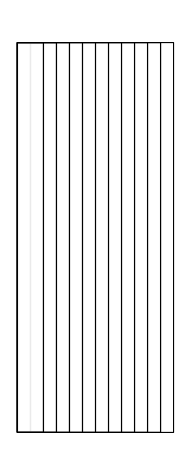

```mathematica
Graphics[{FaceForm@Opacity[.2, White],EdgeForm@Black,Rectangle@@@boxes}]
```

```mathematica
Differences[boxes]
```

{{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{-1,0},{-1,0}},{{0,0},{0,0}},{{0,0},{-1,0}},{{0,0},{0,0}},{{0,0},{-1,0}},{{0,0},{0,0}},{{0,0},{-1,0}},{{0,0},{0,0}},{{0,0},{-1,0}},{{0,0},{0,0}},{{0,0},{-1,0}},{{0,0},{0,0}}}

```mathematica
Total[Differences[]]
```

{{-10,0},{-10,0}}

```mathematica
Length[]
```

21

### Clean up. Build out of composites.

```mathematica
GraphicsRow/@Transpose[{CellularAutomatonHistoryPlot["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},30,"Margin"-> 3]&/@{"Ecologist","Schick engine"},CellularAutomatonPlot3D["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},60]&/@{"Ecologist","Schick engine"},CellularAutomatonSpacetimePlot["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},60]&/@{"Ecologist","Schick engine"}}]
```

{-Graphics-,-Graphics-}

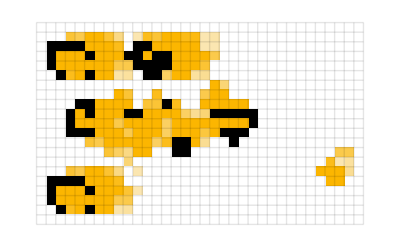
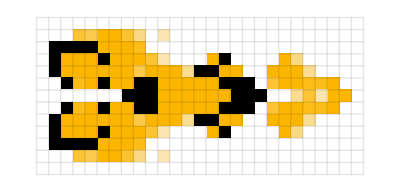
Ecologist | -Graphics- | -Graphics- | -Graphics3D- | -Graphics-
Schick engine | -Graphics- | -Graphics- | -Graphics3D- | -Graphics-

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"Static"->{100, 100},{"Trails",10,.9}->{Automatic, 80},{"3D",60}->{100, 100},{"Spacetime", 60}->75}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{1.5, 1.5}]&@ {"Ecologist","Schick engine"}
```

### Fix y scale labels have √□ symbols Annotate points by having them be little lines (usually vertical) Add back in colors

#### V1

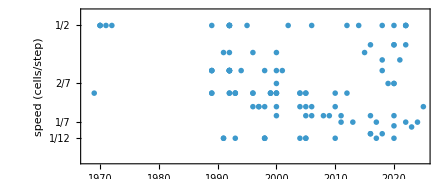

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotMarkers->{Graphics[Line[{{0,0},{0,1}}]],8}]]
```

```mathematica
data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]
```

{{1969,1/4},{1970,1/2},{1970,1/2},{1970,1/2},{1971,1/2},{1972,1/2},{1989,1/4},{1989,1/3},{1989,1/2},{1989,1/3},{1989,1/4},{1989,1/3},{1991,1/12},{1991,1/12},{1991,2/5},{1992,1/3},{1992,1/3},{1992,1/3},{1992,1/2},{1992,2/5},{1992,1/3},{1992,1/3},{1992,1/3},{1992,1/3},{1992,1/2},{1992,1/4},{1992,1/2},{1992,1/2},{1992,1/4},{1992,1/2},{1993,1/12},{1993,1/4},{1993,1/4},{1993,1/4},{1994,1/3},{1995,1/2},{1996,1/4},{1996,2/5},{1996,1/5},{1996,1/4},{1997,1/5},{1997,1/5},{1998,1/12},{1998,1/12},{1998,1/12},{1998,1/5},{1998,1/3},{1999,1/4},{1999,1/4},{1999,1/4},{2000,1/5},{2000,2/5},{2000,1/3},{2000,1/4},{2000,1/6},{2000,1/4},{2000,2/7},{2000,1/4},{2001,1/3},{2002,1/2},{2004,1/5},{2004,1/4},{2004,1/12},{2004,1/4},{2005,1/4},{2005,1/12},{2005,1/12},{2005,1/5},{2005,1/4},{2005,1/6},{2006,1/6},{2006,1/5},{2006,1/2},{2008,1/6},{2009,1/6},{2010,1/5},{2010,1/12},{2010,1/4},{2011,1/6},{2011,1/7},{2012,1/4},{2012,1/2},{2013,1/7},{2014,1/2},{2015,2/5},{2016,1/6},{2016,1/10},{2016,1/10},{2016,3/7},{2017,1/12},{2017,1/7},{2018,1/3},{2018,1/10},{2018,1/2},{2018,(√5)/6},{2019,2/7},{2020,2/7},{2020,1/6},{2020,1/12},{2020,3/7},{2020,2/7},{2020,31/240},{2020,3/7},{2020,1/2},{2021,(√5)/6},{2022,3/7},{2022,1/2},{2022,1/2},{2022,1/2},{2022,1/7},{2023,1/8},{2024,1/7},{2025,1/5}}

```mathematica
Select[$LifeData,#Class==="Spaceship"&]
```

```mathematica
Values[Select[$LifeData,#Class==="Spaceship"&&#Year == 2018&& #[["Speed"]] === 1/2&]]
```

{<|Name→MWSS behind Coe ship,Year→2018,Class→Spaceship,Period→4,Speed→Rational[1,2],Wiki→https://conwaylife.com/wiki/MWSS_behind_Coe_ship,DataFiles→{mwssbehindcoeship.cells,mwssbehindcoeship.rle},MatrixData→SparseArray[Automatic,{27,18},0,{1,{{0,0,0,0,0,0,0,0,0,7,10,12,14,22,24,24,24,26,30,34,36,36,36,36,36,36,36,36},{{6},{7},{12},{13},{14},{15},{16},{4},{11},{17},{3},{10},{3},{17},{3},{4},{5},{6},{7},{8},{9},{10},{8},{9},{4},{5},{3},{4},{6},{7},{4},{5},{6},{7},{5},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→36|>}

```mathematica
Select[Values[Select[$LifeData,#Class==="Spaceship"&]], Times@@Dimensions[#MatrixData]<15000&]
```

```mathematica
as =Map[
If[Times@@Dimensions[#MatrixData]<15000, Line[{{0, 0}, #}]&[getvector[#]],Line[{{0, 0}, {0, 1}}]] &,Values[Select[$LifeData,#Class==="Spaceship"&]]];
```

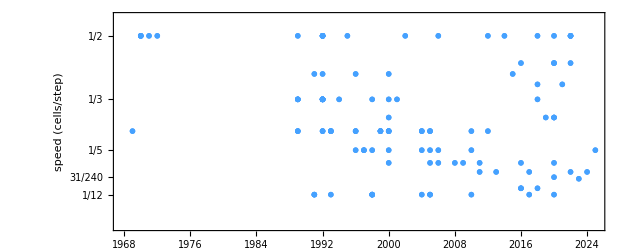

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[List/@Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Graphics[#, PlotRange->{{-1, 1}, {-1, 1}}], 30}&/@as)]]
```

{-Graphics-,-Graphics-}

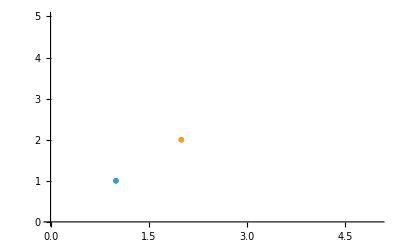

-Graphics-

```mathematica
ListPlot[List/@Table[{i, i}, {i, 2}], PlotMarkers->Echo@Take[Graphics[#, PlotRange->{{-1, 1}, {-1, 1}}]&/@as, 2], PlotRange->{{0, 5}, {0, 5}}]
```

```mathematica
Take[as, 2]
```

{Line[{{0,0},{1/4,-1/4}}],Line[{{0,0},{-1/2,0}}]}

```mathematica
List/@Take[as, 2]
```

{{Line[{{0,0},{1/4,-1/4}}]},{Line[{{0,0},{-1/2,0}}]}}

```mathematica
ListPlot[List/@Table[{i, i}, {i, 2}], PlotMarkers->Take[as, 2], PlotRange->{{0, 5}, {0, 5}}]
```

-Graphics-

```mathematica
Length[{Graphics[#], 8}&/@as]
```

113

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55}]]
```

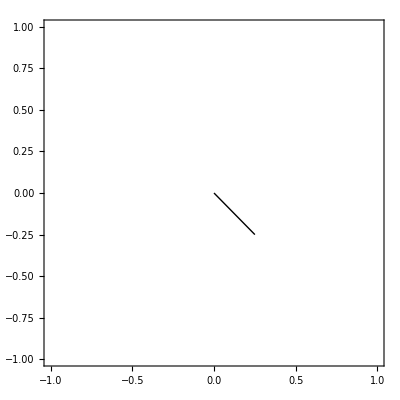
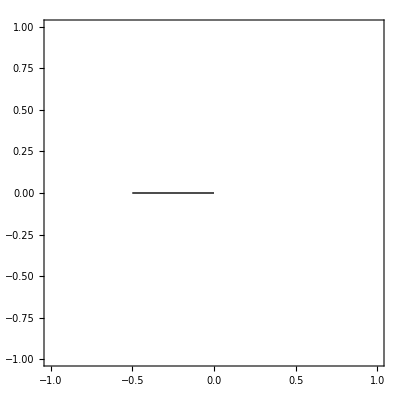
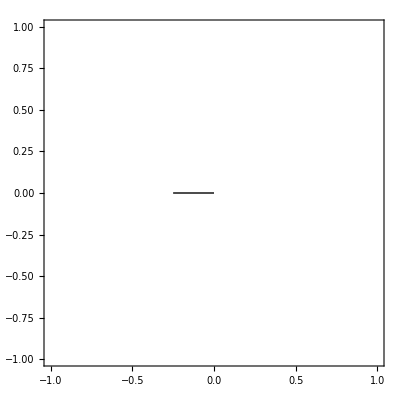
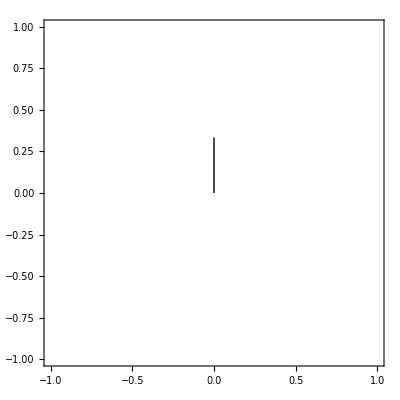
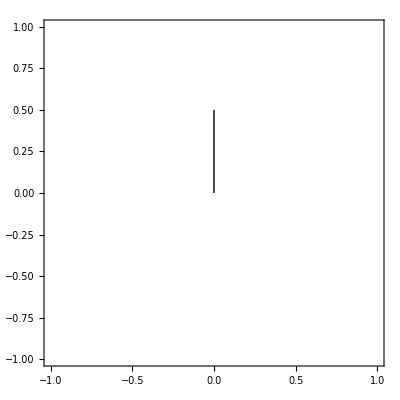
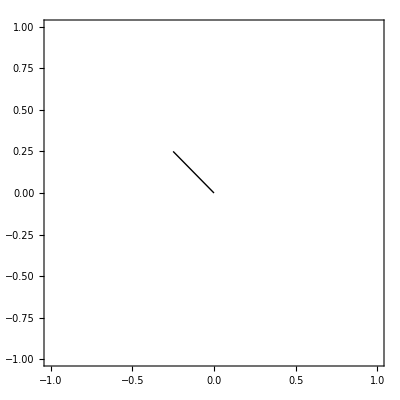
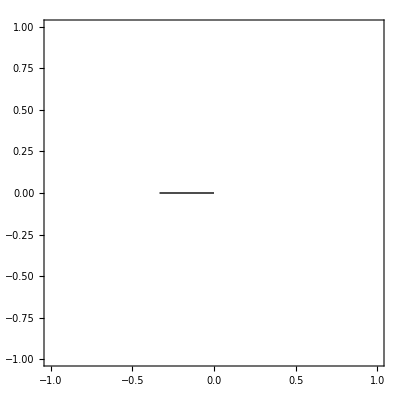
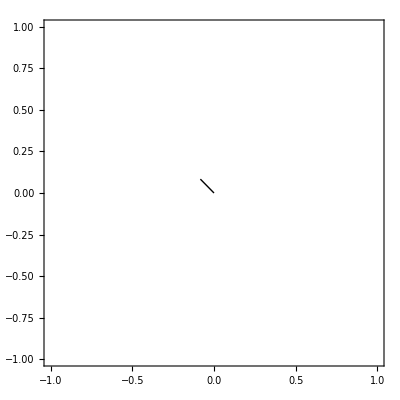
{{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8},{-Graphics-,8}}

```mathematica
{Graphics[#, Frame->True, FrameTicks->True, PlotRange->{{-1, 1}, {-1, 1}}], 8}&/@as
```

#### V2

Something is wrong here, and I can’t figure out what, I will come back to it

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Graphics[#, PlotRange->{{-1, 1}, {-1, 1}}], 30}&/@as)]]
```

-Graphics-

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000, Line[{{0, 0}, #}]&[getvector[#]],Line[{{0, 0}, {0, 1}}]] &,Values[Select[$LifeData,#Class==="Spaceship"&]]];
```

```mathematica
hists  = CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100], "Decay"-> .9]&/@ Select[Values[Select[$LifeData,#Class==="Spaceship"&]], Times@@Dimensions[#MatrixData]<10000&];
```

```mathematica
smallas =
Map[
If[Times@@Dimensions[#MatrixData]<10000, Line[{{0, 0}, #}]&[getvector[#]],Line[{{0, 0}, {0, 1}}]] &,
Select[Values[Select[$LifeData,#Class==="Spaceship"&]], Times@@Dimensions[#MatrixData]<10000&]];
```

```mathematica
Transpose[{Graphics/@as, hists}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
{Graphics[Arrow[{{0, 0}, #}]&[getvector[#]], PlotRange->{{-1,1}, {-1, 1}}], CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10#Period, "Decay"-> .9], #Speed}&/@Take[Values[Select[$LifeData,#Class==="Spaceship"&]], {60, 80}]
```

{{-Graphics-,-Graphics-,1/2},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/2},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/7}}

### Try to have spaceships go in the same direction [and/or show arrows]

Also requested to sort by direction in addition to period

For Developer

#### Garbage

```mathematica
byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==3&],#Year&],#Year&]]
```

{<|Name→84P3H1V0.1,Year→1989,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/84P3H1V0.1,DataFiles→{84p3h1v0.1.cells,84p3h1v0.1.rle},MatrixData→SparseArray[Automatic,{8,41},0,{1,{{0,4,24,36,50,68,74,80,84},{{8},{15},{27},{34},{6},{7},{8},{9},{10},{14},{15},{17},{18},{19},{23},{24},{25},{27},{28},{32},{33},{34},{35},{36},{2},{3},{4},{6},{13},{20},{22},{29},{36},{38},{39},{40},{1},{10},{12},{13},{14},{18},{20},{22},{24},{28},{29},{30},{32},{41},{2},{5},{11},{13},{14},{15},{18},{19},{20},{22},{23},{24},{27},{28},{29},{31},{37},{40},{6},{17},{18},{24},{25},{36},{4},{5},{17},{25},{37},{38},{15},{17},{25},{27}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→84|>,<|Name→Turtle,Year→1989,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/Turtle,DataFiles→{turtle.cells,turtle.rle},MatrixData→SparseArray[Automatic,{10,12},0,{1,{{0,4,11,15,19,22,25,29,33,40,44},{{2},{3},{4},{12},{2},{3},{6},{8},{9},{11},{12},{4},{5},{6},{11},{2},{5},{7},{11},{1},{6},{11},{1},{6},{11},{2},{5},{7},{11},{4},{5},{6},{11},{2},{3},{6},{8},{9},{11},{12},{2},{3},{4},{12}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→44|>,<|Name→25P3H1V0.1,Year→1989,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/25P3H1V0.1,DataFiles→{25p3h1v0.1.cells,25p3h1v0.1.rle},MatrixData→SparseArray[Automatic,{5,16},0,{1,{{0,3,11,18,23,25},{{8},{9},{11},{5},{6},{8},{10},{11},{13},{14},{15},{2},{3},{4},{5},{8},{9},{16},{1},{6},{10},{14},{15},{2},{3}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→25|>,<|Name→Fly,Year→1992,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/Fly,DataFiles→{fly.cells,fly.rle},MatrixData→SparseArray[Automatic,{20,34},0,{1,{{0,1,3,8,14,19,31,43,53,62,73,82,92,103,113,123,134,144,149,154,157},{{3},{2},{4},{2},{4},{27},{29},{33},{2},{26},{27},{29},{31},{34},{12},{13},{14},{23},{33},{1},{2},{12},{13},{16},{18},{19},{23},{26},{27},{28},{29},{2},{4},{14},{15},{16},{17},{20},{22},{25},{26},{31},{32},{2},{3},{12},{15},{19},{20},{21},{27},{28},{29},{3},{11},{16},{19},{20},{23},{24},{27},{30},{4},{7},{11},{16},{19},{20},{21},{23},{25},{30},{31},{8},{10},{11},{16},{19},{20},{21},{22},{28},{5},{6},{10},{11},{16},{19},{20},{21},{22},{28},{5},{7},{11},{16},{19},{20},{21},{23},{25},{30},{31},{4},{5},{11},{16},{19},{20},{23},{24},{27},{30},{5},{7},{12},{15},{19},{20},{21},{27},{28},{29},{6},{14},{15},{16},{17},{20},{22},{25},{26},{31},{32},{12},{13},{16},{18},{19},{23},{26},{27},{28},{29},{12},{13},{14},{23},{33},{26},{27},{29},{31},{34},{27},{29},{33}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→157|>,<|Name→60P3H1V0.3,Year→1992,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/60P3H1V0.3,DataFiles→{60p3h1v0.3.cells,60p3h1v0.3.rle},MatrixData→SparseArray[Automatic,{8,33},0,{1,{{0,4,10,27,44,55,57,59,60},{{13},{15},{16},{17},{5},{12},{18},{25},{26},{28},{3},{4},{5},{6},{11},{12},{15},{17},{18},{22},{23},{25},{27},{28},{30},{31},{32},{2},{3},{7},{9},{10},{13},{14},{15},{16},{18},{19},{20},{21},{22},{25},{26},{33},{1},{5},{7},{8},{9},{10},{19},{23},{27},{31},{32},{5},{20},{6},{11},{10}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→60|>,<|Name→Brain,Year→1992,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/Brain,DataFiles→{brain.cells,brain.rle},MatrixData→SparseArray[Automatic,{11,17},0,{1,{{0,6,14,20,30,34,40,48,56,62,68,70},{{2},{3},{4},{14},{15},{16},{1},{3},{5},{6},{12},{13},{15},{17},{1},{3},{5},{13},{15},{17},{2},{4},{5},{7},{8},{10},{11},{13},{14},{16},{6},{8},{10},{12},{4},{6},{8},{10},{12},{14},{3},{4},{6},{8},{10},{12},{14},{15},{3},{4},{5},{8},{10},{13},{14},{15},{3},{4},{7},{11},{14},{15},{2},{7},{8},{10},{11},{16},{2},{16}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→70|>,<|Name→Dart,Year→1992,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/Dart,DataFiles→{dart.cells,dart.rle},MatrixData→SparseArray[Automatic,{10,15},0,{1,{{0,1,3,5,8,8,12,16,22,26,34},{{8},{7},{9},{6},{10},{7},{8},{9},{5},{6},{10},{11},{3},{7},{9},{13},{2},{3},{7},{9},{13},{14},{1},{7},{9},{15},{2},{4},{5},{7},{9},{11},{12},{14}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→34|>,<|Name→25P3H1V0.2,Year→1992,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/25P3H1V0.2,DataFiles→{25p3h1v0.2.cells,25p3h1v0.2.rle},MatrixData→SparseArray[Automatic,{8,16},0,{1,{{0,1,7,10,15,19,21,24,25},{{11},{9},{10},{11},{13},{14},{15},{8},{9},{16},{3},{7},{10},{14},{15},{2},{3},{4},{5},{1},{5},{2},{4},{7},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→25|>,<|Name→Edge-repair spaceship 1,Year→1992,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/Edge-repair_spaceship_1,DataFiles→{edgerepairspaceship1.cells,edgerepairspaceship1.rle},MatrixData→SparseArray[Automatic,{7,16},0,{1,{{0,1,5,11,18,22,25,26},{{9},{8},{9},{10},{11},{3},{7},{11},{12},{14},{15},{2},{3},{4},{5},{11},{14},{15},{1},{5},{13},{16},{2},{4},{7},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→26|>,<|Name→233P3H1V0,Year→1994,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/233P3H1V0,DataFiles→{233p3h1v0.cells,233p3h1v0.rle},MatrixData→SparseArray[Automatic,{36,31},0,{1,{{0,13,23,31,37,43,51,59,63,71,75,75,79,83,91,103,111,116,121,125,131,133,135,147,157,167,173,179,183,189,197,203,209,213,223,229,233},{{9},{10},{11},{12},{13},{15},{16},{17},{19},{20},{21},{22},{23},{8},{9},{10},{13},{15},{17},{19},{22},{23},{24},{7},{12},{13},{15},{17},{19},{20},{25},{11},{14},{15},{17},{18},{21},{6},{13},{15},{17},{19},{26},{6},{7},{12},{14},{18},{20},{25},{26},{6},{7},{9},{10},{22},{23},{25},{26},{10},{13},{19},{22},{4},{5},{10},{12},{20},{22},{27},{28},{6},{11},{21},{26},{5},{6},{26},{27},{2},{3},{29},{30},{2},{3},{6},{7},{25},{26},{29},{30},{1},{6},{7},{8},{9},{10},{22},{23},{24},{25},{26},{31},{7},{9},{11},{12},{20},{21},{23},{25},{8},{9},{16},{23},{24},{10},{15},{16},{17},{22},{10},{12},{20},{22},{11},{12},{15},{17},{20},{21},{13},{19},{10},{22},{7},{8},{10},{11},{12},{13},{19},{20},{21},{22},{24},{25},{7},{8},{10},{12},{14},{18},{20},{22},{24},{25},{7},{9},{12},{14},{15},{17},{18},{20},{23},{25},{12},{14},{15},{17},{18},{20},{11},{12},{13},{19},{20},{21},{10},{14},{18},{22},{10},{12},{13},{19},{20},{22},{9},{10},{13},{14},{18},{19},{22},{23},{8},{9},{12},{20},{23},{24},{6},{7},{9},{23},{25},{26},{5},{7},{25},{27},{2},{3},{5},{9},{10},{22},{23},{27},{29},{30},{2},{3},{5},{27},{29},{30},{2},{4},{28},{30}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→233|>,<|Name→Wasp,Year→1998,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/Wasp,DataFiles→{wasp.cells,wasp.rle},MatrixData→SparseArray[Automatic,{9,22},0,{1,{{0,2,9,15,24,33,37,43,44,47},{{11},{15},{8},{10},{12},{13},{15},{16},{17},{7},{10},{17},{18},{20},{21},{2},{3},{6},{7},{10},{14},{17},{20},{21},{2},{3},{5},{7},{8},{11},{14},{19},{22},{1},{5},{10},{11},{1},{3},{5},{8},{11},{12},{10},{2},{3},{4}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→47|>,<|Name→54P3H1V0,Year→2018,Class→Spaceship,Period→3,Speed→Rational[1,3],Wiki→https://conwaylife.com/wiki/54P3H1V0,DataFiles→{54p3h1v0.cells,54p3h1v0.rle},MatrixData→SparseArray[Automatic,{13,13},0,{1,{{0,2,3,9,14,19,24,27,37,40,46,48,51,54},{{4},{6},{6},{1},{3},{7},{8},{10},{11},{1},{2},{7},{8},{12},{2},{6},{8},{9},{13},{2},{6},{8},{9},{12},{2},{7},{9},{2},{3},{4},{5},{6},{7},{8},{10},{11},{12},{3},{11},{12},{5},{6},{7},{8},{9},{10},{3},{4},{3},{6},{7},{3},{6},{7}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→54|>}

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{{2,3,4,5,6,7,8,9,10},{12,15,16,20,21,30,36}},Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  -Graphics-
-Graphics-period 12  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 20  
-Graphics-
-Graphics-period 21  
-Graphics-
-Graphics-period 30  
-Graphics-
-Graphics-period 36

```mathematica
p3=Drop[SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==16&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],{-2}];
```

```mathematica
Select[$LifeData,#Class==="Oscillator"&&#Period==16&]
```

```mathematica
bydirperiod = SortBy[GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<#[["Period"]]<60&]], {#Period, getvector[#]}&], #[[1, "Period"]]&];
```

```mathematica
bydirperiod[[1]]
```

{<|Name→Glider,Year→1969,Class→Spaceship,Period→4,Speed→Rational[1,4],Wiki→https://conwaylife.com/wiki/Glider,DataFiles→{glider.cells,glider.rle},MatrixData→SparseArray[Automatic,{3,3},0,{1,{{0,1,2,5},{{2},{3},{1},{2},{3}}},{1,1,1,1,1}}],InitialWeight→5|>}

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,MeshStyle->Opacity[.07]]&/@(Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@bydirperiod)[[4]]
```

{-Graphics-}

```mathematica
Length[Partition[bydirperiod, 19]]
```

2

```mathematica
Partition[]
```

```mathematica
Graphics[{Style[Text["Hello", {-1, 0}], Large], as[[1]]}]
```

-Graphics-

```mathematica
Row[Column[Labeled[Column[{Row[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0],Left]&/@(Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydirperiod[[;;21]],bydirperiod[[22;;]]}]
```

-Graphics-2018
-Graphics--Graphics-
-Graphics-1989
-Graphics--Graphics-
-Graphics-1989
-Graphics--Graphics-
-Graphics-1969
-Graphics--Graphics-
-Graphics-1996
-Graphics--Graphics-
-Graphics-1989-Graphics-1992
-Graphics--Graphics-
-Graphics-1970-Graphics-1970
-Graphics--Graphics-
-Graphics-2004-Graphics-1989-Graphics-1999-Graphics-1993-Graphics-2000
-Graphics--Graphics-
-Graphics-1996
-Graphics--Graphics-
-Graphics-1997
-Graphics--Graphics-
-Graphics-2000-Graphics-2006-Graphics-2005
-Graphics--Graphics-
-Graphics-2000-Graphics-1991
-Graphics--Graphics-
-Graphics-2000
-Graphics--Graphics-
-Graphics-2012
-Graphics--Graphics-
-Graphics-2000
-Graphics--Graphics-
-Graphics-2005
-Graphics--Graphics-
-Graphics-2018
-Graphics--Graphics-
-Graphics-2009-Graphics-2008
-Graphics--Graphics-
-Graphics-2013
-Graphics--Graphics-
-Graphics-2011
-Graphics--Graphics-
-Graphics-2024-Graphics-2017-Graphics-2022
-Graphics--Graphics--Graphics-2000
-Graphics--Graphics-
-Graphics-2020-Graphics-2020-Graphics-2016
-Graphics--Graphics-
-Graphics-2002
-Graphics--Graphics-
-Graphics-2022
-Graphics--Graphics-
-Graphics-2010
-Graphics--Graphics-
-Graphics-2023
-Graphics--Graphics-
-Graphics-1992-Graphics-2001
-Graphics--Graphics-
-Graphics-2004
-Graphics--Graphics-
-Graphics-2016
-Graphics--Graphics-
-Graphics-2022
-Graphics--Graphics-
-Graphics-1972
-Graphics--Graphics-
-Graphics-1997
-Graphics--Graphics-
-Graphics-1995
-Graphics--Graphics-
-Graphics-1971
-Graphics--Graphics-
-Graphics-2006
-Graphics--Graphics-
-Graphics-2020
-Graphics--Graphics-
-Graphics-1998
-Graphics--Graphics-
-Graphics-2014
-Graphics--Graphics-

#### sorting by year and direction

```mathematica
bydirperiod = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<#[["Period"]]<60&]], {#Period, getvector[#]}&]), #[[1, "Period"]]&];
```

```mathematica
Map[#Year&, im, {2}]
```

{{2000},{2020,2020,2016},{2002},{2022},{2010},{2023},{1992,2001},{2004},{2016},{2022},{1972},{1997},{1995},{1971},{2006},{2020},{1998},{2014}}

```mathematica
Row[Column[Labeled[Column[{Row[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},3#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0],Left]&/@ (im =Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydirperiod[[;;21]],bydirperiod[[22;;]]}]
```

-Graphics-2018
-Graphics--Graphics-
-Graphics-1989
-Graphics--Graphics-
-Graphics-1989
-Graphics--Graphics-
-Graphics-1969
-Graphics--Graphics-
-Graphics-1996
-Graphics--Graphics-
-Graphics-1989-Graphics-1992
-Graphics--Graphics-
-Graphics-1970-Graphics-1970
-Graphics--Graphics-
-Graphics-2004-Graphics-1989-Graphics-1999-Graphics-1993-Graphics-2000
-Graphics--Graphics-
-Graphics-1996
-Graphics--Graphics-
-Graphics-1997
-Graphics--Graphics-
-Graphics-2000-Graphics-2006-Graphics-2005
-Graphics--Graphics-
-Graphics-2000-Graphics-1991
-Graphics--Graphics-
-Graphics-2000
-Graphics--Graphics-
-Graphics-2012
-Graphics--Graphics-
-Graphics-2000
-Graphics--Graphics-
-Graphics-2005
-Graphics--Graphics-
-Graphics-2018
-Graphics--Graphics-
-Graphics-2009-Graphics-2008
-Graphics--Graphics-
-Graphics-2013
-Graphics--Graphics-
-Graphics-2011
-Graphics--Graphics-
-Graphics-2024-Graphics-2017-Graphics-2022
-Graphics--Graphics--Graphics-2000
-Graphics--Graphics-
-Graphics-2020-Graphics-2020-Graphics-2016
-Graphics--Graphics-
-Graphics-2002
-Graphics--Graphics-
-Graphics-2022
-Graphics--Graphics-
-Graphics-2010
-Graphics--Graphics-
-Graphics-2023
-Graphics--Graphics-
-Graphics-1992-Graphics-2001
-Graphics--Graphics-
-Graphics-2004
-Graphics--Graphics-
-Graphics-2016
-Graphics--Graphics-
-Graphics-2022
-Graphics--Graphics-
-Graphics-1972
-Graphics--Graphics-
-Graphics-1997
-Graphics--Graphics-
-Graphics-1995
-Graphics--Graphics-
-Graphics-1971
-Graphics--Graphics-
-Graphics-2006
-Graphics--Graphics-
-Graphics-2020
-Graphics--Graphics-
-Graphics-1998
-Graphics--Graphics-
-Graphics-2014
-Graphics--Graphics-

#### Now attempting to rotate so all go down

```mathematica
bydir = SortBy[GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], #Period&], #[[1, "Period"]]&];
```

```mathematica
VectorAngle[{1, 0}, {1/4, 1/4}]
```

π/4

```mathematica
PlanarAngle[{0, 0}->{{1/4, 0}, {1/4, 1/4}}]
```

π/4

```mathematica
Graphics[Arrow[{{0, 0}, {1/4, #}}]&/@  {1/4,0, - 1/4}]
```

-Graphics-

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},10#Period,"Decay"-> .85,PlotRangePadding->{0, 0},ImageSize->10 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]],VectorAngle[{1, 0}, Echo@getvector[#]]} &/@bydir[[{1}, 1]]
```

{0,1/2}

{{-Graphics-,π/2}}

So we need to rotate these so they all go down, question is how? So how do we

π/4

```mathematica
AngleVector
```

```mathematica
Row[Column[Labeled[Column[{Row[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},3#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],Left]&/@(Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydirperiod[[;;21]],bydirperiod[[22;;]]}]
```

#### V2 Rotate

```mathematica
bydir = SortBy[GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], #Period&], #[[1, "Period"]]&];
```

```mathematica
AngleVector[Pi/2]
```

{0,1}

```mathematica
vec
```

{0,1/2}

```mathematica
Map[Module[{ }, 
vec =getvector[#];
angle= If[MemberQ[vec, 0],  -Pi/2 - PlanarAngle[{0, 0}->{{1, 0},vec}], 0];
{Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->10 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], angle], vec} ]&,bydir, {2}]
```

{{{-Graphics-,{0,1/2}},{-Graphics-,{-1/2,0}}},{{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}},{-Graphics-,{1/3,0}},{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}},{-Graphics-,{1/3,0}},{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}},{-Graphics-,{-1/3,0}}},{{-Graphics-,{-1/4,-1/4}},{-Graphics-,{1/2,0}},{-Graphics-,{1/2,0}},{-Graphics-,{1/2,0}},{-Graphics-,{1/4,0}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/2,0}},{-Graphics-,{1/4,0}},{-Graphics-,{1/2,0}},{-Graphics-,{1/2,0}},{-Graphics-,{1/4,0}},{-Graphics-,{1/2,0}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{0,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,0}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{1/4,1/4}},{-Graphics-,{0,1/4}},{-Graphics-,{1/2,0}},{-Graphics-,{1/2,0}},{-Graphics-,{1/2,0}}},{{-Graphics-,{0,2/5}},{-Graphics-,{0,2/5}},{-Graphics-,{0,2/5}},{-Graphics-,{1/5,0}},{-Graphics-,{0,1/5}},{-Graphics-,{1/5,1/5}},{-Graphics-,{0,2/5}},{-Graphics-,{1/5,1/5}},{-Graphics-,{1/5,1/5}},{-Graphics-,{1/5,1/5}},{-Graphics-,{0,2/5}},{-Graphics-,{0,1/5}}},{{-Graphics-,{0,1/3}},{-Graphics-,{1/6,0}},{-Graphics-,{1/6,1/6}},{-Graphics-,{1/6,0}},{-Graphics-,{0,1/6}},{-Graphics-,{0,1/6}},{-Graphics-,{1/6,1/6}},{-Graphics-,{0,1/2}},{-Graphics-,{0,1/6}},{-Graphics-,{1/6,1/3}},{-Graphics-,{0,1/6}},{-Graphics-,{1/6,1/3}}},{{-Graphics-,{0,2/7}},{-Graphics-,{1/7,1/7}},{-Graphics-,{1/7,0}},{-Graphics-,{0,3/7}},{-Graphics-,{0,1/7}},{-Graphics-,{0,2/7}},{-Graphics-,{0,2/7}},{-Graphics-,{0,3/7}},{-Graphics-,{0,3/7}},{-Graphics-,{0,3/7}},{-Graphics-,{0,1/7}},{-Graphics-,{0,1/7}}},{{-Graphics-,{1/2,0}},{-Graphics-,{0,1/4}},{-Graphics-,{0,1/2}},{-Graphics-,{1/8,1/8}}},{{-Graphics-,{0,1/3}},{-Graphics-,{0,1/3}}},{{-Graphics-,{0,1/5}},{-Graphics-,{0,1/10}},{-Graphics-,{0,1/10}},{-Graphics-,{0,1/10}}},{{-Graphics-,{1/2,0}},{-Graphics-,{0,1/2}}},{{-Graphics-,{0,1/5}}},{{-Graphics-,{-1/2,0}}},{{-Graphics-,{1/2,0}},{-Graphics-,{0,1/2}}},{{-Graphics-,{0,2/7}}},{{-Graphics-,{0,1/5}}},{{-Graphics-,{0,1/2}}}}

```mathematica
Map[
With[{vec = getvector[#]}, 
{Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], 
If[MemberQ[vec, 0], -Pi/2, If[MemberQ[vec, 1/4], -Pi/4, PlanarAngle[{0, 0}->{{1, 0},vec}]]] -PlanarAngle[{0, 0}->{{1, 0},vec}]], If[MemberQ[vec, 0], 3Pi/2, If[MemberQ[vec, 1/4], 7Pi/4, PlanarAngle[{0, 0}->{{1, 0},vec}]]] -PlanarAngle[{0, 0}->{{1, 0},vec}], vec}] &,bydir, {2}]
```

{{{-Graphics-,π,{0,1/2}},{-Graphics-,π/2,{-1/2,0}}},{{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}},{-Graphics-,(3 π)/2,{1/3,0}},{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}},{-Graphics-,(3 π)/2,{1/3,0}},{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}},{-Graphics-,π/2,{-1/3,0}}},{{-Graphics-,0,{-1/4,-1/4}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/4,0}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/4,0}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/4,0}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,π,{0,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,0}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,(3 π)/2,{1/4,1/4}},{-Graphics-,π,{0,1/4}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,(3 π)/2,{1/2,0}}},{{-Graphics-,π,{0,2/5}},{-Graphics-,π,{0,2/5}},{-Graphics-,π,{0,2/5}},{-Graphics-,(3 π)/2,{1/5,0}},{-Graphics-,π,{0,1/5}},{-Graphics-,0,{1/5,1/5}},{-Graphics-,π,{0,2/5}},{-Graphics-,0,{1/5,1/5}},{-Graphics-,0,{1/5,1/5}},{-Graphics-,0,{1/5,1/5}},{-Graphics-,π,{0,2/5}},{-Graphics-,π,{0,1/5}}},{{-Graphics-,π,{0,1/3}},{-Graphics-,(3 π)/2,{1/6,0}},{-Graphics-,0,{1/6,1/6}},{-Graphics-,(3 π)/2,{1/6,0}},{-Graphics-,π,{0,1/6}},{-Graphics-,π,{0,1/6}},{-Graphics-,0,{1/6,1/6}},{-Graphics-,π,{0,1/2}},{-Graphics-,π,{0,1/6}},{-Graphics-,0,{1/6,1/3}},{-Graphics-,π,{0,1/6}},{-Graphics-,0,{1/6,1/3}}},{{-Graphics-,π,{0,2/7}},{-Graphics-,0,{1/7,1/7}},{-Graphics-,(3 π)/2,{1/7,0}},{-Graphics-,π,{0,3/7}},{-Graphics-,π,{0,1/7}},{-Graphics-,π,{0,2/7}},{-Graphics-,π,{0,2/7}},{-Graphics-,π,{0,3/7}},{-Graphics-,π,{0,3/7}},{-Graphics-,π,{0,3/7}},{-Graphics-,π,{0,1/7}},{-Graphics-,π,{0,1/7}}},{{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,π,{0,1/4}},{-Graphics-,π,{0,1/2}},{-Graphics-,0,{1/8,1/8}}},{{-Graphics-,π,{0,1/3}},{-Graphics-,π,{0,1/3}}},{{-Graphics-,π,{0,1/5}},{-Graphics-,π,{0,1/10}},{-Graphics-,π,{0,1/10}},{-Graphics-,π,{0,1/10}}},{{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,π,{0,1/2}}},{{-Graphics-,π,{0,1/5}}},{{-Graphics-,π/2,{-1/2,0}}},{{-Graphics-,(3 π)/2,{1/2,0}},{-Graphics-,π,{0,1/2}}},{{-Graphics-,π,{0,2/7}}},{{-Graphics-,π,{0,1/5}}},{{-Graphics-,π,{0,1/2}}}}

```mathematica
Map[
With[{vec =getvector[#]}, 
{CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], 
(If[MemberQ[vec, 0], -Pi/2 , If[MemberQ[vec, 1/4], -Pi/4, PlanarAngle[{0, 0}->{{1, 0},vec}]]]- PlanarAngle[{0, 0}->{{1, 0},vec}])], vec, PlanarAngle[{0, 0}->{{1, 0},vec}]}] &,bydir, {2}]
```

{{{-Graphics-,-Graphics-,{0,1/2},π/2},{-Graphics-,-Graphics-,{1/2,0},0}},{{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{-1/3,0},π},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{-1/3,0},π},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{1/3,0},0}},{{-Graphics-,-Graphics-,{1/4,-1/4},(7 π)/4},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{0,1/4},π/2},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{0,1/4},π/2},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π}},{{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{-1/5,0},π},{-Graphics-,-Graphics-,{0,1/5},π/2},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{0,1/5},π/2}},{{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{-1/6,0},π},{-Graphics-,-Graphics-,{-1/6,1/6},(3 π)/4},{-Graphics-,-Graphics-,{-1/6,0},π},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{-1/6,1/6},(3 π)/4},{-Graphics-,-Graphics-,{0,1/2},π/2},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{-1/6,1/3},ArcCos[-1/(√5)]},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{-1/6,1/3},ArcCos[-1/(√5)]}},{{-Graphics-,-Graphics-,{0,2/7},π/2},{-Graphics-,-Graphics-,{-1/7,1/7},(3 π)/4},{-Graphics-,-Graphics-,{-1/7,0},π},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,1/7},π/2},{-Graphics-,-Graphics-,{0,2/7},π/2},{-Graphics-,-Graphics-,{0,2/7},π/2},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,1/7},π/2},{-Graphics-,-Graphics-,{0,1/7},π/2}},{{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{0,1/4},π/2},{-Graphics-,-Graphics-,{0,1/2},π/2},{-Graphics-,-Graphics-,{-1/8,1/8},(3 π)/4}},{{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2}},{{-Graphics-,-Graphics-,{0,1/5},π/2},{-Graphics-,-Graphics-,{0,1/10},π/2},{-Graphics-,-Graphics-,{0,1/10},π/2},{-Graphics-,-Graphics-,{0,1/10},π/2}},{{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{0,1/2},π/2}},{{-Graphics-,-Graphics-,{0,1/5},π/2}},{{-Graphics-,-Graphics-,{1/2,0},0}},{{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{0,1/2},π/2}},{{-Graphics-,-Graphics-,{0,2/7},π/2}},{{-Graphics-,-Graphics-,{0,1/5},π/2}},{{-Graphics-,-Graphics-,{0,1/2},π/2}}}

#### V3

```mathematica
Map[
With[{vec =getvector[#]}, 
{CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], 
If[(!MemberQ[vec, 0]) &&(!SameQ@@Abs[vec]),If[vec[[2]] >0, -Pi,  0] ,(If[MemberQ[vec, 0], -Pi/2 , If[SameQ@@Abs[vec],  -Pi/4, 0]]- PlanarAngle[{0, 0}->{{1, 0},vec}])]], vec, PlanarAngle[{0, 0}->{{1, 0},vec}]}] &,bydir, {2}]
```

{{{-Graphics-,-Graphics-,{0,1/2},π/2},{-Graphics-,-Graphics-,{1/2,0},0}},{{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{-1/3,0},π},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{-1/3,0},π},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{1/3,0},0}},{{-Graphics-,-Graphics-,{1/4,-1/4},(7 π)/4},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{0,1/4},π/2},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,0},π},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{-1/4,1/4},(3 π)/4},{-Graphics-,-Graphics-,{0,1/4},π/2},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{-1/2,0},π}},{{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{-1/5,0},π},{-Graphics-,-Graphics-,{0,1/5},π/2},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{-1/5,1/5},(3 π)/4},{-Graphics-,-Graphics-,{0,2/5},π/2},{-Graphics-,-Graphics-,{0,1/5},π/2}},{{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{-1/6,0},π},{-Graphics-,-Graphics-,{-1/6,1/6},(3 π)/4},{-Graphics-,-Graphics-,{-1/6,0},π},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{-1/6,1/6},(3 π)/4},{-Graphics-,-Graphics-,{0,1/2},π/2},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{-1/6,1/3},ArcCos[-1/(√5)]},{-Graphics-,-Graphics-,{0,1/6},π/2},{-Graphics-,-Graphics-,{-1/6,1/3},ArcCos[-1/(√5)]}},{{-Graphics-,-Graphics-,{0,2/7},π/2},{-Graphics-,-Graphics-,{-1/7,1/7},(3 π)/4},{-Graphics-,-Graphics-,{-1/7,0},π},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,1/7},π/2},{-Graphics-,-Graphics-,{0,2/7},π/2},{-Graphics-,-Graphics-,{0,2/7},π/2},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,3/7},π/2},{-Graphics-,-Graphics-,{0,1/7},π/2},{-Graphics-,-Graphics-,{0,1/7},π/2}},{{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{0,1/4},π/2},{-Graphics-,-Graphics-,{0,1/2},π/2},{-Graphics-,-Graphics-,{-1/8,1/8},(3 π)/4}},{{-Graphics-,-Graphics-,{0,1/3},π/2},{-Graphics-,-Graphics-,{0,1/3},π/2}},{{-Graphics-,-Graphics-,{0,1/5},π/2},{-Graphics-,-Graphics-,{0,1/10},π/2},{-Graphics-,-Graphics-,{0,1/10},π/2},{-Graphics-,-Graphics-,{0,1/10},π/2}},{{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{0,1/2},π/2}},{{-Graphics-,-Graphics-,{0,1/5},π/2}},{{-Graphics-,-Graphics-,{1/2,0},0}},{{-Graphics-,-Graphics-,{-1/2,0},π},{-Graphics-,-Graphics-,{0,1/2},π/2}},{{-Graphics-,-Graphics-,{0,2/7},π/2}},{{-Graphics-,-Graphics-,{0,1/5},π/2}},{{-Graphics-,-Graphics-,{0,1/2},π/2}}}

```mathematica
Map[
With[{vec =getvector[#]}, 
Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], 
If[(!MemberQ[vec, 0]) &&(!SameQ@@Abs[vec]),If[vec[[2]] >0, -Pi,  0] ,(If[MemberQ[vec, 0], -Pi/2 , If[SameQ@@Abs[vec],  -Pi/4, 0]]- PlanarAngle[{0, 0}->{{1, 0},vec}])]]] &,bydir, {2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Map[With[{vec =Echo[getvector[#]]}, 
{CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]], Rotate[
CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},5#Period,"Decay"-> .8,PlotRangePadding->{0, 0},ImageSize->5 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},
#Period]]],Mesh->True,MeshStyle->Opacity[.1]],
If[vec[[2]]>0, Pi, 0]]}]&, bydir[[;;1]], {2}]
```

{0,1/2}

{1/2,0}

{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

```mathematica
{0,-1} - Sign[{1/2,0} ]
```

{-1,-1}

```mathematica
PlanarAngle[{0, 0}->{{1, 0},{-1,-1}}]
```

(5 π)/4

#### Final byperiod

```mathematica
byperiod = SortBy[#, #Year&]&/@GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], #Period&];
```

```mathematica
Map[#Year&, byperiod, {2}]
```

{{1969,1970,1970,1970,1989,1989,1992,1992,1992,1992,1992,1992,1993,1993,1993,1996,1996,1999,1999,1999,2000,2000,2000,2004,2004,2005,2005,2012,2018,2020,2022},{1971,2006},{1972,2022},{1989,1989,1989,1992,1992,1992,1992,1992,1992,1994,1998,2018},{1989,1992},{1991,1992,1996,1996,1997,2000,2000,2005,2006,2010,2015,2025},{1992,2001},{1995},{1997},{1998},{2000,2000,2005,2006,2008,2009,2011,2012,2016,2018,2020,2021},{2000,2011,2013,2016,2017,2019,2020,2020,2020,2022,2022,2024},{2002,2010,2022,2023},{2004,2016,2016,2018},{2014},{2020}}

```mathematica
Row[Column[Labeled[Column[{Row[
Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},3#Period]]],Mesh->True,MeshStyle->Opacity[.1]], getangle[getvector[#]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0],Left]&/@ (Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydir[[;;9]],bydir[[10;;]]}]
```

-Graphics-1989
-Graphics--Graphics-
-Graphics-1989
-Graphics--Graphics-
-Graphics-1969
-Graphics--Graphics-
-Graphics-2000-Graphics-1991
-Graphics--Graphics-
-Graphics-2009-Graphics-2000
-Graphics--Graphics-
-Graphics-2013-Graphics-2000
-Graphics--Graphics-
-Graphics-2002
-Graphics--Graphics-
-Graphics-1992-Graphics-2001
-Graphics--Graphics-
-Graphics-2004-Graphics-2016
-Graphics--Graphics--Graphics-2022-Graphics-1972
-Graphics--Graphics-
-Graphics-1997
-Graphics--Graphics-
-Graphics-1995
-Graphics--Graphics-
-Graphics-1971-Graphics-2006
-Graphics--Graphics-
-Graphics-2020
-Graphics--Graphics-
-Graphics-1998
-Graphics--Graphics-
-Graphics-2014
-Graphics--Graphics-

#### Final by direction and period

```mathematica
bydirperiod = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<#[["Period"]]<60&]], {#Period, getvector[#]}&]), #[[1, "Period"]]&];
```

```mathematica
Row[Column[Labeled[Column[{GraphicsRow[
Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},3#Period]]],Mesh->True,MeshStyle->Opacity[.1]], getangle[getvector[#]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0],Left]&/@ (Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydirperiod[[;;10]],bydir[[11;;]]}]
```

-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
getangle[vec_]:= If[(!MemberQ[vec, 0]) &&(!SameQ@@Abs[vec]),If[vec[[2]] >0, -Pi,  0] ,(If[MemberQ[vec, 0], -Pi/2 , If[SameQ@@Abs[vec],  -Pi/4, 0]]- PlanarAngle[{0, 0}->{{1, 0},vec}])]
```

### Fixing bblg

```mathematica
BoundingBoxLayeredGraph[$LifeData["7-engine Cordership"]]
```

-Graphics-

```mathematica
LayeredGraph[LifeMultiwayGraph[MultiwayLife[InitializeMultiwayLife[First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]],100]]&[$LifeData["7-engine Cordership"]]]
```

-Graphics-

```mathematica
SimpleClosure[
InitializeMultiwayLife[
First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]],100]&[$LifeData["7-engine Cordership"]]//Length
```

97

```mathematica
MultiwayLife[
InitializeMultiwayLife[
First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]],100]&[$LifeData["7-engine Cordership"]]//Length
```

101